```mathematica
(*1*)
ClearAll;
```

```mathematica
f[x_]=x/(x^2+1) Sin[a x]
```

(x Sin[a x])/(1+x^2)

```mathematica
FullSimplify[Series[f[x],{x,0,4},Assumptions->(x>0)]]
```

a x^2-1/6 (a (6+a^2)) x^4+O[x]^5

```mathematica
(*2*)
ClearAll;
```

```mathematica
N[Integrate[Sqrt[x+1],{x,-1,1}],20]
```

1.8856180831641267317

```mathematica
(*3*)
ClearAll;
```

```mathematica
g[x_]=Piecewise[{{Sqrt[x^2+1],x≥0},{Sqrt[-x+1],x<0}}]
```

Piecewise[{{√(1+x^2), x≥0}, {√(1-x), x<0}, {0, True}}]

```mathematica
N[Integrate[g[x],{x,-1,1}]]
```

2.36674

```mathematica
(*4*)
ClearAll;
```

```mathematica
A={{0,1,2,0},{2,1,1,2},{1,1,2,2},{2,2,1,1}}
```

{{0,1,2,0},{2,1,1,2},{1,1,2,2},{2,2,1,1}}

```mathematica
MatrixForm[A]
```

(0 | 1 | 2 | 0
2 | 1 | 1 | 2
1 | 1 | 2 | 2
2 | 2 | 1 | 1)

```mathematica
N[Det[A],4]
```

-3.

```mathematica
N[Eigenvalues[A],4]
```

{5.296,-1.,-0.148+0.738 ⅈ,-0.148-0.738 ⅈ}

```mathematica
(*5*)
ClearAll;
```

```mathematica
FullSimplify[DSolve[{y''[x]+b^2 y[x]==Sin[b x],y[0]==1,y'[0]==0},y[x],x]]
```

{{y[x]→(b (2 b-x) Cos[b x]+Sin[b x])/(2 b^2)}}

```mathematica
(*6*)
ClearAll;
```

```mathematica
A={1,2,3,4,5,6};
B={a,b,c,d,e,f};
```

```mathematica
AB=Table[{A[[i]],B[[i]]},{i,1,Length[A]}]
```

{{1,a},{2,b},{3,c},{4,d},{5,e},{6,f}}

```mathematica
(*7*)
ClearAll;
```

```mathematica
A=RandomReal[{-1,1},100]
```

{0.704784,-0.0498398,-0.509791,0.587679,-0.648426,-0.00954962,0.762624,0.769778,-0.473883,0.325312,0.310886,-0.424187,0.568171,-0.578034,-0.537216,0.733571,-0.967626,0.747834,-0.0184293,-0.961987,-0.675487,0.44086,-0.410812,0.688287,-0.0662267,-0.954942,-0.954997,-0.759917,0.447714,-0.126809,0.533588,-0.484653,0.0885098,-0.49773,0.900394,0.854554,-0.206179,0.434111,0.700618,-0.0740947,0.620401,0.469774,-0.930007,0.552815,0.253499,-0.214698,0.337455,0.087387,0.900401,0.966305,0.248261,0.400715,0.750163,0.479777,0.578506,-0.0737716,-0.426583,-0.28713,-0.798281,-0.625802,0.099111,0.0380527,-0.539484,0.849362,0.296865,0.478675,-0.502188,0.630397,0.221504,0.453799,-0.0337946,0.607002,-0.451868,-0.981421,-0.512473,-0.0522022,0.650758,0.704629,-0.224914,-0.525082,-0.904655,-0.657581,-0.943219,-0.46974,-0.540693,0.697207,-0.942477,0.662353,-0.048881,0.732365,-0.624975,0.712049,0.774468,-0.393005,0.744872,-0.301264,-0.956818,0.0475462,0.896705,0.660225}

```mathematica
(*8*)
ClearAll;
```

```mathematica
A=Table[RandomChoice[{-1,1}],100]
```

{-1,-1,1,1,-1,-1,-1,1,-1,-1,-1,1,-1,-1,-1,-1,-1,-1,1,-1,1,1,-1,-1,1,1,-1,-1,-1,-1,-1,1,-1,1,1,-1,1,-1,-1,1,-1,1,-1,-1,1,1,1,-1,1,-1,-1,1,1,-1,-1,1,1,1,-1,1,1,-1,1,1,-1,-1,1,1,1,-1,1,-1,1,1,-1,-1,-1,-1,-1,1,1,1,-1,1,-1,-1,1,1,-1,-1,-1,1,1,1,1,1,-1,1,-1,-1}

```mathematica
(*9*)
ClearAll;
```

```mathematica
FullSimplify[DSolve[{y''[x]+y[x]^3+y[x]==0,y[0]==0,y'[0]==1},y[x],x]][[1]]
```

{y[x]→-ⅈ √(1+√3) JacobiSN[ⅈ √(1/2 (-1+√3)) x,-2-√3]}

```mathematica
y1[x_]=y[x]/.%
```

-ⅈ √(1+√3) JacobiSN[ⅈ √(1/2 (-1+√3)) x,-2-√3]

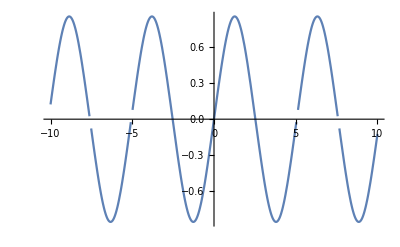

```mathematica
Plot[y1[x],{x,-10,10}]
```

```mathematica
(*10*)
ClearAll;
```

```mathematica
A={{0,0.1},{1,0.2},{1.5,0.4},{2,0.5},{2.5,0.4},{3,0.44},{4,0.55},{5,0.7}};
```

```mathematica
f=Interpolation[A]
```

InterpolatingFunction[…]

```mathematica
f[2.35]
```

0.43077

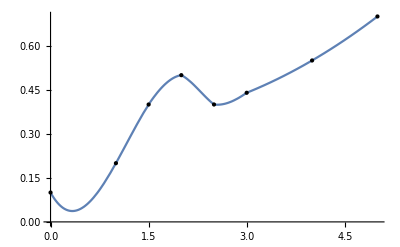

```mathematica
Plot[f[x],{x,0,5},Epilog->Point[A]]
```

```mathematica
(*11*)
ClearAll;
```

```mathematica
eq1=x^2+y^2==1;
eq2= y Exp[x]==x;
```

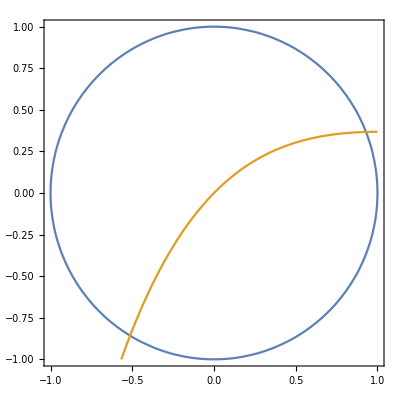

```mathematica
ContourPlot[{x^2+y^2==1, y Exp[x]==x},{x,-1,1},{y,-1,1}]
```

```mathematica
N[Solve[{eq1,eq2},{y,x},Reals]]
```

{{y→0.366942,x→0.930244},{y→-0.858096,x→-0.513489}}

```mathematica
(*12*)
ClearAll;
```

```mathematica
y[x_,a_]=x-x Exp[-x+a]
```

x-ⅇ^(a-x) x

```mathematica
x1[a_]=x/.FullSimplify[Solve[D[y[x,a],x]==0,x]][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1-ProductLog[ⅇ^(1-a)]

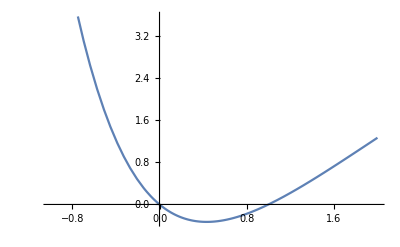

```mathematica
Plot[y[x,1],{x,-1,2}]
```

```mathematica
N[x1[1]]
```

0.432857

```mathematica
(*13*)
ClearAll;
```

```mathematica
DecimalForm[NIntegrate[Sqrt[x^2+x+1]/(x^2+1),{x,0,1},Method->"LocalAdaptive",MaxRecursion->19, PrecisionGoal->10],DefaultPrintPrecision->11]
```

1.0155898789